## Lesson

Interpret natural language:

```mathematica
Interpreter["City"]["nyc"]
```

New York City

Find cases of a given type of object in text:

```mathematica
TextCases["Choose between $5, €5 and ¥5000","CurrencyAmount"]
```

{$5,€5,¥5000}

Break down a sentence’s structure:

```mathematica
TextStructure["You can do so much with the Wolfram Language."]
```

You
Pronoun
Noun Phrase  can
Verb  do
Verb  so
Adverbmuch
Adverb
Adverb Phrase  with
Preposition  the
DeterminerWolfram
Proper NounLanguage
Proper Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence

Translate word into given language:

```mathematica
WordTranslation["beer","Czech"]
```

{pivo}

## Questions

Q1. Use Interpreter to find the location of the Eiffel Tower.

```mathematica
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

Q2. Use Interpreter to find a university referred to as “U of T”.

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

Q3. Use Interpreter to find the chemicals referred to as C2H4, C2H6 and C3H8.

```mathematica
Interpreter["Chemical"]/@{"C2H4","C2H6","C3H8"}
```

{ethylene,ethane,propane}

Q4. Use Interpreter to interpret the date “20140108”.

```mathematica
Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

Q5. Find universities that can be referred to as “U of X”, where x is any letter of the alphabet.

```mathematica
Interpreter["University"]["U of "<>#]&/@ToUpperCase[Alphabet[]]/.Failure->Nothing
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

Q6. Find which US state capital names can be interpreted as movie titles (use CommonName to get the string versions of entity names).

```mathematica
Interpreter["Movie"]/@CommonName[EntityClass["AdministrativeDivision","AllUSStatesPlusDC"][EntityProperty["AdministrativeDivision","CapitalCity"]]]/.Failure->Nothing
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

Q7. Find cities that can be referred to by permutations of the letters a, i, l and m.

```mathematica
Interpreter["City"][StringJoin[#]]&/@Permutations[Characters["ailm"]]/.Failure->Nothing
```

{Alim,Amli,Balm,Ilam,Lami,Lima,Lamai,Mali,Milah,Mali}

Q8. Make a word cloud of country names in the Wikipedia article on “gunpowder”.

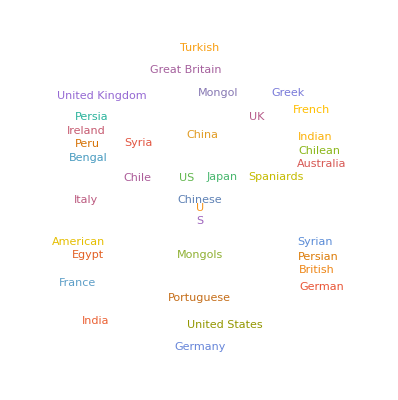

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

Q9. Find all nouns in “She sells seashells by the sea shore”.

```mathematica
TextCases["She sells seashells by the sea shore","Noun"]
```

{seashells,sea,shore}

Q10. Use TextCases to find the number of nouns, verbs and adjectives in the first 1000 characters of the Wikipedia article on computers.

```mathematica
TextCases[StringTake[WikipediaData["computers"],1000],#]&/@{"Noun","Verb","Adjective"}
```

{{computer,machine,sequences,arithmetic,operations,computation,computers,sets,operations,programs,programs,computers,range,tasks,term,computer,system,computer,hardware,system,software,equipment,operation,group,computers,computer,network,computer,cluster,range,consumer,products,computers,control,systems,devices,microwave,ovens,controls,factory,devices,robots,Computers,core,devices,computers,devices,smartphones,Computers,power,Internet,billions,computers,users},{is,can,be,programmed,carry,can,perform,known,enable,perform,may,refer,includes,operating,needed,used,are,linked,function,use,including,are,links},{logical,digital,electronic,generic,wide,complete,peripheral,full,such,broad,industrial,simple,special-purpose,remote,industrial,general-purpose,such,personal,mobile,such}}

Q11. Find the grammatical structure of the first sentence of the Wikipedia article about computers.

```mathematica
TextStructure[TextSentences[WikipediaData["computers"]][[1]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

Q12. Find the 10 most common nouns in ExampleData[{“Text”, “AliceInWonderland”}]

```mathematica
Keys[TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]]
```

{Rabbit,door,voice,time,Mouse,way,moment,thing,head,garden}

Q13. Make a community graph plot of the graph representation of the text structure of the first sentence of the Wikipedia article about language.

```mathematica
CommunityGraphPlot[TextStructure[TextSentences[WikipediaData["language"]][[1]],"ConstituentGraphs"][[1]]]
```

-Graphics-

Q14. Make a list of numbers of nouns, verbs, adjectives and adverbs found by WordList in English.

```mathematica
Length[WordList[#]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{24493,6503,11392,3120}

Q15. Generate a list of the translations of numbers 2 through 10 into French.

```mathematica
Flatten[WordTranslation[IntegerName[Range[2,10]],"French"]]
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}